# Verjetnost

Verjetnosti poskus je poskus, katerega rezultat je odvisen od naključja.
Osnovne rezultate poskusa imenujemo izidi.
Dogodek je pojav, ki se lahko zgodi znotraj poskusa. Lahko ga zapišemo kot množico izidov, ki so za ta dogodek ugodni.
Poznamo tudi nemogoče dogodke in gotove dogodke. Nemogoči dogodek označimo z N in ga predstavlja prazna množica. Gotovi dogotek označimo z G in ga predstavlja množica vseh mogočih izidov znotraj poskusa.

## Računanje z dogodki

Produkt ali presek dogodkov A in B je dogodek, ki se zgodi, kadar se zgodita dogodka A in B hkrati. Množico ugodnih izidov bi torej predstavili kot presek množic A in B oziroma  A  ∩  B. Če se dogodka A in B ne moreta zgoditi hkrati, rečemo, da sta nezdružjiva. Njun produkt je nemogoč dogodek (N). 

Unija dogodkov A in B je dogodek, ki se zgodi kadar se zgodi dogodek A ali dogodek B, ali pa oba hkrati. Množico ugodnih izidov bi torej predstavili kot unijo množic A in B oziroma  A ∪ B.

Nasprotni dogodek danega dogodka A je dogodek, ki se zgodi takrat kadar se dogodek A ne zgodi. Množico ugodnih izidov bi torej predstavili kot komplement množice A oziroma A’.

## Verjetnost dogodka

Vzemimo poskus, ki ima vse izide enakovredne. To pomeni, da se pri dovolj velikem številu ponovitev poskusa vsi izidi pojavljajo v povprečju enako pogosto.

Verjetnost dogodka A je torej razmerje med številom ugodnih izidov in številom vseh možnih izidov.

P(A) = (število ugodnih izidov)/(število vseh možnih izidov)

oziroma:

P(A) = m/n

Vemo, da je verjetnost nemogočega dogodka (N) enaka 0. Verjetnost gotovega dogodka (G) pa je enaka 1. Verjetnost poljubnega dogodka torej vedno leži na intervalu med 0 in 1 oziroma [0, 1].

### Verjetnost nasprotnega dogodka:

P(A’) = 1 - P(A) oziroma P(A) + P(A’) = 1

### Verjetnost unije dogodkov:

P(A ∪ B) = P(A) + P(B) - P(A × B)

### Verjetnost unije nezdružjivih dogodkov:

P(A ∪ B) = P(A) + P(B)

### Verjetnost produkta neodvisnih dogodkov:

P(A × B) = P(A) × P(B)

### Verjetnost produkta odvisnih dogodkov:

P(A × B) = P(A) × P(B / A)

## Računski primeri

Poglejmo recimo poker. Specifično texas hold ‘em. Vsak igralec v roke dobi dve karti, na mizo pa jih pade vsega skupaj 5. Zmaga tisti, ki drži najmočnejšo kombinacijo svojih dveh kart z tremi kartami na mizi, ali pa najboljšo kombinacijo ene karte iz roke in štirih iz mize. Možnosti kombinacij od najslabše do najboljše so: visoka karta, en par, dva para, tris, lestvica, barva, full house, poker oz. four of a kind, barvna lestvica in najmnočnejša kraljeva lestvica. 

Kakšne so torej verjetnosti, da dobimo katero izmed zgoraj naštetih kombinacij? Da bi računali naprej, moramo najprej poznati število vseh možnih kombinacij z 5-imi kartami iz kupčka 52-ih kart. To bomo izračunali tako:

```mathematica
n = 52;
```

```mathematica
m = 5;
```

```mathematica
Binomial[n,m]
```

2598960

Torej število vseh možnih kombinacij 5-ih kart iz kupčka 52-ih kart je 2 598 960.

### Royal Flush (Kraljeva lestvica)

Poglejmo, na koliko načinov lahko dobimo kraljevo lestvico. Imamo štiri obleke(srce, karo, pik, križ) v vsaki pa nam je ugoden samo eden dogodek. (10, J, Q, K, A).

```mathematica
m = Binomial[4,1];
```

```mathematica
n = Binomial[52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

0.0001539%

Verjetnost, da se to zgodi je zelo mala. 0.000154% oziroma 649,740 proti 1, kar pomeni, da lahko kraljevo lestvico pričakujemo nekje enkrat v 649,740 poskusih.

### Straight Flush (Barvna lestvica)

Izračunajmo še verjetnost za barvno lestvico. Po principu je ista kot kraljeva lestvica, torej 5 zaporednih kart iste obleke, samo da velja za vse karte, ne samo za 10, J, Q, K, A.

```mathematica
m = Binomial[10,1] * Binomial[4,1] - Binomial[4,1];
```

```mathematica
n = Binomial[52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

0.001385%

Torej verjetnost, da se to zgodi, je seveda večja od verjetnosti dogodka royal flusha. 0.00139% oziroma 72,192 proti 1, kar pomeni da lahko barvno lestvico pričakujemo nekje enkrat v 72,192 poskusih.

### Four of a kind (Poker)

Poker je kombinacija štirih istih kart. Recimo KKKK, ali AAAA. Kakšna je verjetnost, da pade?

```mathematica
m = Binomial[13,1] * Binomial[12,1] * Binomial[4,1];
```

```mathematica
n = Binomial[52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

0.02401%

Da se to zgodi je verjetnost torej 0.0240% oziroma 4,165 proti 1, kar pomeni da poker lahko pričakujemo nekje enkrat v 4,165 poskusih. Po rezultatih vidimo, da verjetnost občutno narašča v korelaciji z vse slabšimi “rokami”.

### Full House

```mathematica
m = Binomial[13,1]*Binomial[4,3]*Binomial[12,1]*Binomial[4,2];
```

```mathematica
n = Binomial[52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

0.1441%

### Flush (Barva)

```mathematica
m = Binomial[13,5]*Binomial[4,1]-Binomial[10,1]*Binomial[4,1];
```

```mathematica
n = Binomial[52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

0.1965%

### Straight (Lestvica)

```mathematica
m = Binomial[10,1]*Binomial[4,1]^5 - Binomial[10,1]*Binomial[4,1];
```

```mathematica
n = Binomial[52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

0.3925%

### Three of a kind (Tris)

```mathematica
m = Binomial[13,1]*Binomial[4,3]*Binomial[12,2]*Binomial[4,1]^2;
```

```mathematica
n = Binomial[52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

2.113%

### Two pair (Dva para)

```mathematica
m = Binomial[13,2]*Binomial[4,2]^2*Binomial[11,1]*Binomial[4,1];
```

```mathematica
n = Binomial [52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

4.754%

### One pair (En par)

```mathematica
m = Binomial[13,1]*Binomial[4,2]*Binomial[12,3]*Binomial[4,1]^3;
```

```mathematica
n = Binomial[52,5];
```

```mathematica
P = N[m/n];
```

```mathematica
PercentForm[P]
```

42.26%

### High card (Visoka karta)

Da dobimo nič, oziroma da imamo samo visoko karto pa je verjetnost seveda 100% oziroma 1.

Poglejmo še graf padanja verjetnosti (ordinata) v odvisnosti od moči “rok” v pokru.

```mathematica
n = Range[100];
```

```mathematica
P = N[m/n];
```

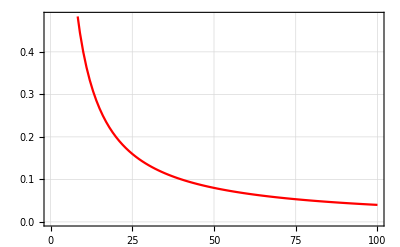

```mathematica
ListLinePlot[P,PlotStyle->RGBColor[1.,0.,0.],PlotTheme->"Detailed"]
```

## PROBLEM ROJSTNEGA DNE

Recimo, da mečemo kovanec in stavimo, na cifro. Ker je enako verjetno, da pade cifra ali glava je verjetnost da pade cifra torej 50%. Če bi vedno stavili na cifro, to pomeni, da bi načeloma na dolgi rok zmagali polovico metov. 

Kaj pa če bi kdo želel staviti na to, da imata vsaj dva v razredu rojstni dan na isti dan?
Vprašanje je bolj kompleksno kot se zdi. Verjetnost, da imata vsaj dva v skupini ljudi (n) je seveda odvisna od velikosti te skupine. Če sta v skupini samo dva človeka, bi bili verjetno presenečeni, če bi imela na isti dan rojstni dan. Torej kako velika mora biti skupina ljudi (n), da bi verjetnost, da imata vsaj dva na isti dan rojstni dan zrastla na 50%?

Pri tem problemu bomo zanemarili prestopna leta. Predpostavili bomo torej, da je vsako leto dolgo točno 365 dni. Predpostavili bomo tudi, da je vsak dan enako primeren za rojstni dan, kot ostali. 

Začnemo tako, da izračunamo verjetnost, da imata dva človeka na isti dan rojstni dan. Skupina ljudi (n) bo sestavljena torej iz dveh ljudi.
Prvi človek ima lahko katerikoli rojstni dan. Ima 365 možnosti od 365 dni.
Torej je verjetnost (365/365) kar pa je enako 1. Verjetnost, da ima drugi človek na isti dan rojstni dan pa je (1/365), ker ima na voljo samo en specifičen dan. Da izračunamo verjetnost, da imata oba isti rojstni dan moramo verjetnosti med sabo pomnožiti:

```mathematica
P = N[(365/365)*(1/365)];
```

```mathematica
PercentForm[P]
```

0.274%

Verjetnost, da imata v skupini dveh naključno izbranih ljudi oba na isti dan rojstni dan je torej približno 0.274%.
Kaj pa če so v skupini ljudi trije ljudje?
Verjetnost, da imata prva dva rojstni dan na isti dan je torej 1/365. Lahko pa imata skupni rojstni dan tudi prvi in tretji, ali pa imajo rojstni dan vsi trije na isti dan. Stvari se hitro zakomplicirajo.

Da bi rešili problem, moramo poznati eno od osnovnih pravil verjetnosti. To je, da je verjetnost vedno vrednost med 0 in 1 in da je vsota verjetnosti da se dogodek zgodi in verjetnosti da se dogodek ne zgodi vedno enaka 1.

P(dogodek se zgodi) + P(dogodek se ne zgodi) = 1
oziroma:
P(imata vsaj dva skupni rd) + P(nimata niti dva) = 1
iz tega sledi:
P(imata vsaj dva skupni rd) = 1 - P(nimata niti dva)

Kakšna je torej verjetnost, da nimata niti dva človeka na isti dan rojstni dan?
Vemo, da ima lahko prvi rojstni dan na katerikoli dan. Drugi človek pa mora imeti rojstni dan na drug dan kot prvi. Torej je opcij 364, verjetnost pa 364/365. Za tretjega 363/365 in tako naprej.
Izračunamo verjetnost, da drugi in tretji nimata rojstni dan na isti dan:

```mathematica
P = N[(365/365)*(364/365)*(363/365)];
```

```mathematica
PercentForm[P]
```

99.18%

Verjetnost, da drugi in tretji nimata rojstni dan na isti dan je torej približno 99.18%.
Za skupino štirih ljudi (n = 4) pa je verjetnost, da ni skupnih rojstnih dnevov:

```mathematica
P = N[(365/365)*(364/365)*(363/365)*(362/365)];
```

```mathematica
PercentForm[P]
```

98.36%

Verjetnost, da v skupini štirih ne bo skupnih rojstnih dnevov je torej približno 98.36%.

Tako lahko nadaljujemo kakor dolgo želimo. Formula za verjetnost P(n), da n ljudi ne bo imelo skupnega rojstnega dneva je:

((365 - 1)/365) × ((365 - 2)/365) × ((365 - 3)/365) × ... × ((365 - (n + 1))/365)

kar pa lahko zapišemo tudi kot:

(365!)/((365 - n)! × 365^n)

Verjetnost, da bo vsaj eno ujemanje pa je torej 1 - verjetnost da ujemanja ne bo:

1 - ((365!)/((365 - n)! × 365^n))

Torej kako velika mora biti skupina (n), da bo verjetnost vsaj enega skupnega rojstnega dneva 50%?

Vnašamo različne velikosti skupin ljudi oziroma n-je:
Za skupino petih ljudi:

```mathematica
P = N[1-(365!/((365-5)!*365^5))];
```

```mathematica
PercentForm[P]
```

2.714%

Za skupino petih je torej verjetnost, da imata vsaj dva na isti dan rojstni dan približno 2.714%.
Kaj pa za skupino desetih ljudi?

```mathematica
P = N[1-(365!/((365-10)!*365^10))];
```

```mathematica
PercentForm[P]
```

11.69%

Za skupino desetih pa je verjetnost vsaj enega skupnega rojstnega dne že 11.69%.
Skupina dvajsetih:

```mathematica
P = N[1-(365!/((365-20)!*365^20))];
```

```mathematica
PercentForm[P]
```

41.14%

Za skupino dvajsetih verjetnost enega ujemanja zraste že na 41.14%
50% pa postane pri 23 ljudeh.
Poglejmo:

```mathematica
P = N[1-(365!/((365-23)!*365^23))];
```

```mathematica
PercentForm[P]
```

50.73%

Za skupino 23-ih ljudi je verjetnost, da imata vsaj dva na isti dan rojstni dan približno 50.73%.

Kaj pa recimo pri 70-ih ljudeh?

```mathematica
P = N[1-(365!/((365-70)!*365^70))];
```

```mathematica
PercentForm[P]
```

99.92%

Pri 70-ih ljudeh pa je verjetnost že 99.92%. Torej skoraj 1.

Poglejmo še graf, z različnimi vrednostmi. Y os predstavlja verjetnost, da imata vsaj dva v skupini na isti dan rojstni dan, X os pa velikost skupine ljudi (n).

```mathematica
n = Range[100];
```

```mathematica
P = N[1-(365!/((365-n)!*365^n))];
```

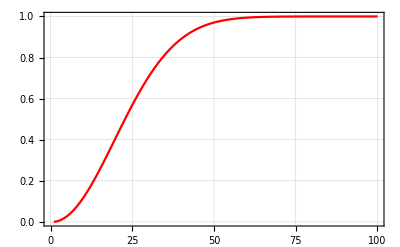

```mathematica
ListLinePlot[P,PlotStyle->RGBColor[1.,0.,0.],PlotTheme->"Detailed"]
```